```mathematica
Clear["Global`*"]
```

```mathematica
fun[x_] := Exp[-2x] +1/3  * Exp[-2/3 *x]
```

```mathematica
fun[x]
```

ⅇ^(-2 x)+1/3 ⅇ^(-2 x/3)

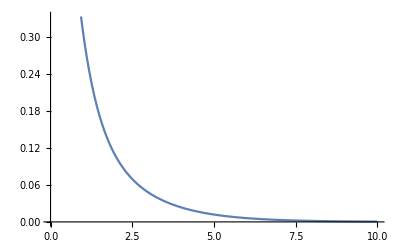

```mathematica
Plot[{fun[k]}, {k,0,10}]
```

```mathematica
invfun[k_] := LaplaceTransform[fun[m],m,k]
```

```mathematica
invfun[x]
```

1/(3 (2/3+x))+1/(2+x)

```mathematica
lambda = 10^{-2};  b = 1 ; theta = 0.1 ; u = 0.5
c = lambda * (1+theta)* Integrate[per*fun[per], {per, 0, Infinity}]
```

0.5

{0.011}

```mathematica
phiinv[k_, c_, theta_, lambda_] := c * (theta/(1+theta)) / (c*k - lambda * (1 - invfun[k]))
```

```mathematica
phiinv[s, c, theta, lambda]
```

{0.001/(0.011 s+1/100 (-1+1/(3 (2/3+s))+1/(2+s)))}

```mathematica
phi[w_]:= InverseLaplaceTransform[phiinv[s, c, theta, lambda], s, w]
```

```mathematica
phi[w]
```

{0.001 (1000.-10.7043 ⅇ^(-1.68567 w)-898.387 ⅇ^(-0.0719075 w))}

```mathematica
psi[w_] := 1 - phi[w]
```

```mathematica
psi[w]
```

{1-0.001 (1000.-10.7043 ⅇ^(-1.68567 w)-898.387 ⅇ^(-0.0719075 w))}

```mathematica
phi[1]
```

{0.161962}

{0.325691}

{0.871268}

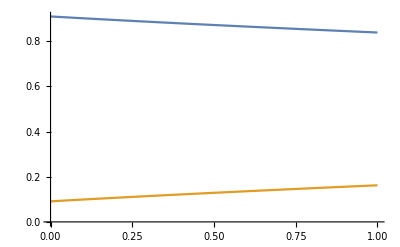

```mathematica
{0.3256905174209238}

psi[0.5]
Plot[{psi[x], phi[x]}, {x, 0,1}]
```

```mathematica
bigx[z_, b_] := (1-psi[z]) / (1-psi[b])
```

```mathematica
bigx[1-z,1]
```

{0.00617427 (1000.-836.054 ⅇ^(0.0719075 z)-1.98373 ⅇ^(1.68567 z))}

```mathematica
pofb := Integrate[bigx[b-x,b]*fun[x],  {x,0,b}]
```

```mathematica
pofb
```

{0.568982}

```mathematica
eud := bigx[u,b] * c/(lambda*(1-pofb))
```

```mathematica
eud
```

{2.02847}